# LP pricing for the BSM model setting

Working directory for output images.

```mathematica
directory= "/Users/scinawa/Dropbox/Apps/Overleaf/Quantum computational finance: martingale asset pricing for incomplete markets/Images/" ;
```

In the next cell we set some parameters (that we don’t want to change in the course of our simulation), such as the number of intervals for discretizing our event space (K in the paper), and ranges of our discretization (-6 to 6 of standard normal gaussian distribution).

```mathematica
k = 100;
xmax = 6;
omegas = Range[-xmax, xmax, (2*xmax)/k];
numericalError = 0;
```

The following are the default value for the parameters that are going to change in the plots:

```mathematica
regularization = 100;
mu = 0.5;
sigma = 1;
pi = 10;
strike = 10;
```

These are the possible values of the discretized standard normal distribution.

```mathematica
N[omegas]
Length[omegas]
```

{-6.,-5.88,-5.76,-5.64,-5.52,-5.4,-5.28,-5.16,-5.04,-4.92,-4.8,-4.68,-4.56,-4.44,-4.32,-4.2,-4.08,-3.96,-3.84,-3.72,-3.6,-3.48,-3.36,-3.24,-3.12,-3.,-2.88,-2.76,-2.64,-2.52,-2.4,-2.28,-2.16,-2.04,-1.92,-1.8,-1.68,-1.56,-1.44,-1.32,-1.2,-1.08,-0.96,-0.84,-0.72,-0.6,-0.48,-0.36,-0.24,-0.12,0.,0.12,0.24,0.36,0.48,0.6,0.72,0.84,0.96,1.08,1.2,1.32,1.44,1.56,1.68,1.8,1.92,2.04,2.16,2.28,2.4,2.52,2.64,2.76,2.88,3.,3.12,3.24,3.36,3.48,3.6,3.72,3.84,3.96,4.08,4.2,4.32,4.44,4.56,4.68,4.8,4.92,5.04,5.16,5.28,5.4,5.52,5.64,5.76,5.88,6.}

101

It’s quite Normal..

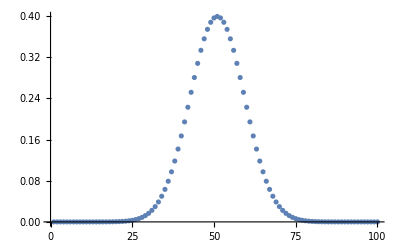

```mathematica
ListPlot[Table[PDF[NormalDistribution[0, 1] , omegas[[i]]] , {i, 1, k}]]
```

```mathematica
DiagonalMatrix[Table[-1, {i, 1,k-1}], 1,k] + DiagonalMatrix[Table[1, {i, 1, k}]];
```

### Analytic formula pricing with BSM

Let’s use the formula on Wikipedia to compute the price of a call option in the BSM model. For this we need some helper functions.

```mathematica
analyticPriceBSM[mu_,  spt_, sigma_,strike_,T_,t_,r_ ] :=Module[{d1, d2,value},
d1 = 1/(sigma*Sqrt[T-t])(Log[spt/strike] + (r+(sigma^2/2))*(T-t)   );
d2 = d1 - sigma*Sqrt[T-t];

(* C(S_0, 0) = N(d_1)S_0 - N(d_2)Ke^{e^-r} *)
value=CDF[NormalDistribution[0,1], d1]*spt -  CDF[NormalDistribution[0,1], d2]*strike*Exp[-r(T-t)];
value
]
```

As an example, let’s compute the price of the derivative with the standard set of parameters:

```mathematica
N[analyticPriceBSM[mu,  pi, sigma,strike,1,0,0]]
```

3.82925

### LP Pricing BSM

Now let’s use our optimization program to compute the value of the LP.
First, we compute the RN derivative, as we do in the paper in section “Linear programming martingale pricing with the Black-Scholes-Merton model”.

```mathematica
getRadonNikodimDerivative[mu_, omegas_, sigma_] := Module[
{},
Table[Exp[-(mu/sigma)*omegas[[i]] - 1/2(mu/sigma)^2], {i, 1, k}] 
]
getRadonNikodimDerivative[mu, omegas, sigma]
```

{17.7254,16.6932,15.721,14.8055,13.9433,13.1313,12.3666,11.6464,10.9682,10.3295,9.72792,9.16141,8.62789,8.12544,7.65225,7.20662,6.78694,6.3917,6.01947,5.66893,5.3388,5.02789,4.73509,4.45934,4.19965,3.95508,3.72475,3.50784,3.30356,3.11117,2.92999,2.75936,2.59867,2.44734,2.30481,2.17059,2.04419,1.92514,1.81303,1.70745,1.60801,1.51437,1.42618,1.34313,1.26491,1.19125,1.12187,1.05654,0.995012,0.937067,0.882497,0.831104,0.782705,0.737123,0.694197,0.65377,0.615697,0.579842,0.546074,0.514274,0.484325,0.45612,0.429557,0.404542,0.380983,0.358796,0.337902,0.318224,0.299692,0.282239,0.265803,0.250324,0.235746,0.222017,0.209088,0.196912,0.185444,0.174645,0.164474,0.154896,0.145876,0.137381,0.12938,0.121846,0.11475,0.108067,0.101774,0.0958472,0.0902655,0.0850088,0.0800583,0.0753961,0.0710054,0.0668703,0.0629761,0.0593087,0.0558548,0.0526021,0.0495388,0.0466538}

This is the main function that solves the linear program given the matrices that we construct in the rest of the file. 
The first parameters are the parameters of the BSM model and the regularization. The parameter minmax specify if you want to solve the minimization or the maximization problem. 
tolz is the numerical tolerance of the LP solver that we use, and method is the (classical) algorithm we use for solving the LP. 

There are two regularization parameters:
- 
- 
Setting the parameter outputQ, it can either output the martingale measure, or the price

```mathematica
optimizationPriceBSM[mu_, pi_, sigma_, omegas_,strike_, regularization_, minmax_, outputQ_, tolz_, methodz_]:= Module[
{regularizingMatrix,regularizationVector,regularizationVector2,ineqMat, ineqVec,
S,sp,mus, pis,p, pNormalized, 
q,dp,derivative,sigmas},

pis = {1} ~ Join ~{pi};
mus = {0} ~Join~ {mu};
sigmas = {0} ~ Join ~{sigma};

(*Build the payoff matrices and the derivative vector*)
S= Table[  
 Table[
pis[[j]]*Exp[sigmas[[j]]*omegas[[i]] + mus[[j]]  - 1/2sigmas[[j]]^2 ] , 
{i,1, k} ] , {j,1, 2} ]  ;

derivative = Table[Max[  S[[2,i]] - strike,  0], {i, 1, k}];

(* Discretize the probability distribution and normalize it *)
p = Table[PDF[NormalDistribution[0, 1] , omegas[[i]]] , {i, 1, k}];   (* Q: why this is normal standard?? *)
pNormalized = p/N[Total[p]];


dp = derivative * pNormalized;
sp = S  * Table[pNormalized, {i, 1, 2}];


regularizingMatrix = DiagonalMatrix[Table[-1, {i, 1,k-1}], 1,k] +(1-mu/sigma*(2*xmax)/k*(1-0.1))*DiagonalMatrix[Table[1, {i, 1, k}]];
regularizationVector = Table[regularization, {i, 1,k-1}] ~ Join ~ {31337};
regularizationVector2 = Table[0, {i, 1,k-1}] ~ Join ~ {0};

ineqMat = ArrayFlatten[{IdentityMatrix[k], regularizingMatrix, -regularizingMatrix}, 1];
ineqVec = ArrayFlatten[{Table[0, {i, 1, k}]-numericalError, regularizationVector2, regularizationVector},1];

q =If[minmax,
LinearOptimization[-dp,{ineqMat,ineqVec}, {sp, -pis } , Tolerance->tolz, Method->methodz],    
 LinearOptimization[dp,{ineqMat,ineqVec}, {sp, -pis } , Tolerance->tolz, Method->methodz] ];

If[outputQ,
q,
q.dp
]
]
```

Let’s show that the function returns a price (if the last variable is True) or the RadonNykodim of the Martingale measure (if the last variable is False)

```mathematica
N[(1-mu/sigma*(2*xmax)/k)]
```

0.94

```mathematica
optimizationPriceBSM[mu, pi, sigma, omegas,strike,0.1, True, True,Automatic, Automatic]
optimizationPriceBSM[mu, pi, sigma, omegas,strike,0.1, True, False,Automatic, Automatic]
```

{27.7656,26.1662,24.6532,23.222,21.868,20.5871,19.3754,18.2291,17.1448,16.1189,15.1485,14.2305,13.3621,12.5405,11.7633,11.0281,10.3326,9.67462,9.05219,8.46337,7.90635,7.37941,6.88092,6.40935,5.96324,5.54123,5.142,4.76433,4.40706,4.06908,3.74935,3.44688,3.16075,2.89007,2.63401,2.39177,2.16262,1.94583,1.74076,1.58608,1.50043,1.41941,1.34276,1.27025,1.20166,1.13677,1.07538,1.01731,0.962376,0.910408,0.861246,0.814738,0.770742,0.729122,0.68975,0.652503,0.617268,0.583936,0.552403,0.522573,0.494354,0.467659,0.442406,0.418516,0.395916,0.374536,0.354311,0.335179,0.317079,0.299957,0.283759,0.268436,0.253941,0.240228,0.227255,0.214984,0.203375,0.192392,0.182003,0.172175,0.162878,0.154082,0.145762,0.137891,0.130444,0.1234,0.116737,0.110433,0.10447,0.0988283,0.0934916,0.088443,0.0836671,0.0791491,0.074875,0.0708318,0.0670069,0.0633885,0.0599655,0.0567274}

3.92119

### Experiments

Helper variable for titling the plots.

```mathematica
title ="Π= "  <> ToString[pi]<> ", μ= " <>ToString[mu] <> ", σ= " <> ToString[sigma] <> ", Z= " <> ToString[strike] <> ", Reg= " <> ToString[regularization];
Print[title]
```

Π= 10, μ= 0.5, σ= 1, Z= 10, Reg= 100

```mathematica
Let's plot the analytic solution of the Radon-Nikodym and the solution of the LP for different regularization values
```

-100 and different for LP Nikodym of solution the^2 values+analytic of plot Radon s solution the^2 Let'

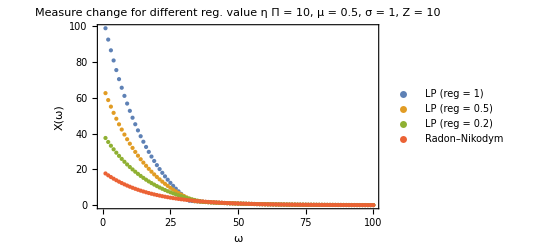

```mathematica
mu = 0.5;
sigma = 1;
pi = 10;
strike = 10;
(*this is the first plot of the paper*)
title ="Π = "  <> ToString[pi]<> ", μ = " <>ToString[mu] <> ", σ = " <> ToString[sigma] <> ", Z = " <> ToString[strike];
regplot= ListPlot[{optimizationPriceBSM[mu, pi, sigma, omegas,strike,1, True, True, Automatic, Automatic],  
optimizationPriceBSM[mu, pi, sigma, omegas,strike,0.5, True, True,Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,0.2, True, True, Automatic, Automatic], 
getRadonNikodimDerivative[mu, omegas, sigma]}, 
PlotStyle->PointSize[Medium],
 PlotLegends->{"LP (reg = 1)", "LP (reg = 0.5)", "LP (reg = 0.2)",  "Radon–Nikodym"},
LabelStyle->{FontSize->13}, Frame->True,FrameLabel->{"ω", "X(ω)"},
PlotRange->All, 
PlotLabel->"Measure change for different reg. value η\n"<> title]
Export[directory <> "regplot.jpg", regplot];
```

Let’s see the difference in L1 norm of the two measures.

```mathematica
measure=optimizationPriceBSM[mu, pi, sigma, omegas,strike,0.06, True, True, Automatic, Automatic];
measureRN=N[getRadonNikodimDerivative[mu, omegas, sigma]];
Norm[measure-measureRN,1]
```

83.7225

```mathematica
pis = {1} ~ Join ~{pi};
mus = {0} ~Join~ {mu};
sigmas = {0} ~ Join ~{sigma};

(*Build the payoff matrices and the derivative vector*)
S= Table[  
 Table[
pis[[j]]*Exp[sigmas[[j]]*omegas[[i]] + mus[[j]]  - 1/2sigmas[[j]]^2 ] , 
{i,1, k} ] , {j,1, 2} ]  ;

derivative = Table[Max[  S[[2,i]] - strike,  0], {i, 1, k}];

(* Discretize the probability distribution and normalize it *)
p = Table[PDF[NormalDistribution[0, 1] , omegas[[i]]] , {i, 1, k}];   (* Q: why this is normal standard?? *)
pNormalized = p/N[Total[p]];


dp = derivative * pNormalized;
sp = S  * Table[pNormalized, {i, 1, 2}];
```

```mathematica
dp.measure
dp.measureRN
```

3.91633

3.82502

```mathematica
pis
```

{1,10}

```mathematica
sp.measure
```

{1.,10.}

#### Scanning regularization parameter

We scan the regularization parameter. We explore this task with three plots. In the first two plots we change the different range of parameters. In the first we create a log-linear plot, where we set \mu to zero.

```mathematica
mu = 0.5;
sigma = 1;
pi = 10;
strike = 10;
```

LinearOptimization::nsolc: There are no points that satisfy the constraints.

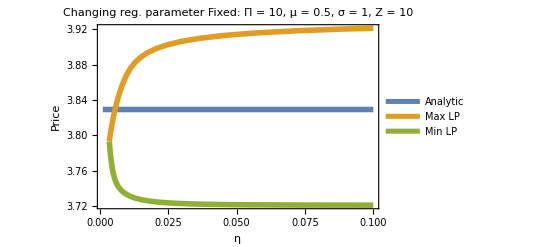

```mathematica
title ="Changing reg. parameter\n Fixed: " <> "Π = "  <> ToString[pi]<> ", μ = " <>ToString[mu] <> ", σ = " <> ToString[sigma] <> ", Z = " <> ToString[strike];
plt1 =Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, True, False,Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, False, False,Automatic, Automatic]}, 
{regularization,0.001, 0.1}, PlotLegends->{"Analytic", "Max LP", "Min LP"},
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01], Thickness[0.01]},
LabelStyle->{FontSize->13}, Frame->True,
FrameLabel->{"η", "Price"}, 
PlotRange->All, PlotLabel->title]
Export[directory <> "plt1.jpg", plt1];
```

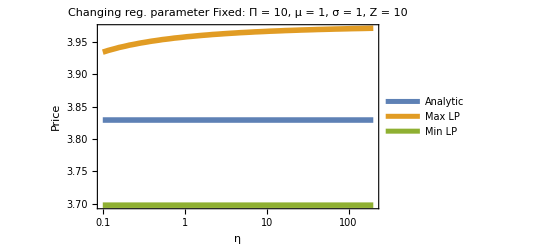

```mathematica
(*Different range *)
mu = 1;
sigma = 1;
pi = 10;
strike = 10;

title ="Changing reg. parameter\n Fixed: " <> "Π = "  <> ToString[pi]<> ", μ = " <>ToString[mu] <> ", σ = " <> ToString[sigma] <> ", Z = " <> ToString[strike];

plt2 =LogLinearPlot[
(*mu_,  spt_, sigma_,strike_,T_,t_,r_*)
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, True, False,Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, False, False,Automatic, Automatic]}, 
{regularization,0.1, 200}, 
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01], Thickness[0.01]},
LabelStyle->{FontSize->13}, Frame->True,
PlotLegends->{"Analytic", "Max LP", "Min LP"},
FrameLabel->{"η", "Price"}, PlotRange->All,  PlotLabel->title]
Export[directory <> "plt2.jpg", plt2];
```

LinearOptimization::nsolc: There are no points that satisfy the constraints.

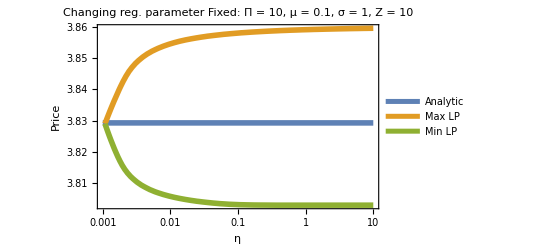

```mathematica
(*setting mu to zero *)
mu = 0.1;
sigma = 1;
pi = 10;
strike = 10;

title ="Changing reg. parameter\n Fixed: " <> "Π = "  <> ToString[pi]<> ", μ = " <>ToString[mu] <> ", σ = " <> ToString[sigma] <> ", Z = " <> ToString[strike];

plt3 =LogLinearPlot[
(*mu_,  spt_, sigma_,strike_,T_,t_,r_*)
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, True, False,Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, False, False,Automatic, Automatic]}, 
{regularization,0.001, 10}, 
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01], Thickness[0.01]},
LabelStyle->{FontSize->13}, Frame->True,
PlotLegends->{"Analytic", "Max LP", "Min LP"},
FrameLabel->{"η", "Price"}, PlotRange->All,  PlotLabel->title]
Export[directory <> "plt3.jpg", plt3];
```

#### Scanning the drift (μ) parameter

In the following, we explore the task with two different regularization parameter. The first plot is the plot that you can find in the paper.

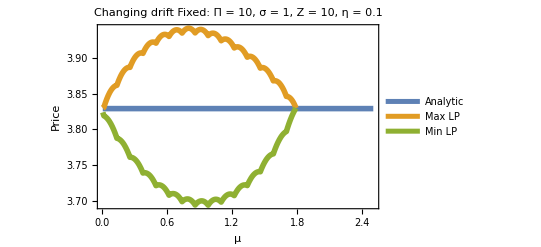

```mathematica
(*Different regularization parameter*)
regularization = 0.1;
mu = 0;
sigma = 1;
pi = 10;
strike = 10;

title ="Changing drift \n Fixed: " <> "Π = "  <> ToString[pi]<> ", σ = " <> ToString[sigma] <> ", Z = " <> ToString[strike] <> ", η = " <> ToString[regularization] ;
pltmu2= Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, True, False,Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, False, False,Automatic, Automatic]}, 
{mu,0.01, 2.5},
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01]},
 PlotLegends->{"Analytic", "Max LP", "Min LP"},FrameLabel->{"μ", "Price"}, LabelStyle->{FontSize->13},Frame->True,PlotRange->All, PlotLabel->title, PlotPoints->200]
Export[directory <> "pltmu2.jpg", pltmu2];
```

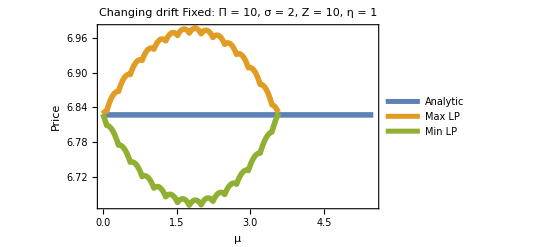

```mathematica
(*Different regularization and sigma parameter*)
regularization = 1;
mu = 0;
sigma = 2;
pi = 10;
strike = 10;

title ="Changing drift \n Fixed: " <> "Π = "  <> ToString[pi]<> ", σ = " <> ToString[sigma] <> ", Z = " <> ToString[strike] <> ", η = " <> ToString[regularization] ;
pltmu2= Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, True, False,Automatic, "InteriorPoint"],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization, False, False,Automatic, "InteriorPoint"]}, 
{mu,0.001, 5.5},
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01]},
 PlotLegends->{"Analytic", "Max LP", "Min LP"},FrameLabel->{"μ", "Price"}, LabelStyle->{FontSize->13},Frame->True,PlotRange->All, PlotLabel->title, PlotPoints->200]
Export[directory <> "pltmu2-sigma.jpg", pltmu2];
```

### Scanning the volatility σ parameter

LinearOptimization::nsolc: There are no points that satisfy the constraints.

LinearOptimization::lpsnf: No solution can be found that satisfies the constraints.

LinearOptimization::nsolc: There are no points that satisfy the constraints.

LinearOptimization::lpsnf: No solution can be found that satisfies the constraints.

LinearOptimization::nsolc: There are no points that satisfy the constraints.

LinearOptimization::lpsnf: No solution can be found that satisfies the constraints.

LinearOptimization::nsolc: There are no points that satisfy the constraints.

LinearOptimization::lpsnf: No solution can be found that satisfies the constraints.

LinearOptimization::nsolc: There are no points that satisfy the constraints.

LinearOptimization::lpsnf: No solution can be found that satisfies the constraints.

LinearOptimization::nsolc: There are no points that satisfy the constraints.

LinearOptimization::lpsnf: No solution can be found that satisfies the constraints.

LinearOptimization::nsolc: There are no points that satisfy the constraints.

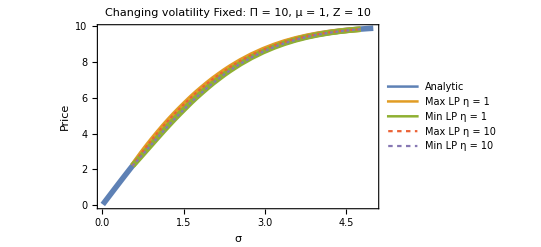

```mathematica
(*regularization = 1;
mu = 1;
sigma = 1;
pi = 10;
strike = 10;
title ="Changing volatility \n Fixed: " <> "Π = "  <> ToString[pi]<> ", μ: " <>ToString[mu] <> ", Z = " <> ToString[strike] <> ", η = " <> ToString[regularization] ;
*)
(*pltsigma=Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,1],
optimizationPriceBSM[mu, pi, sigma, omegas,strike, regularization,True, False],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False]}, 
{sigma, 0.4, 3}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, AxesLabel->{"σ", "Price"}, PlotLabel->title, PlotPoints->200]
Export[directory <> "pltsigma.jpg", pltsigma];

pltsigma2=Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,1],
optimizationPriceBSM[mu, pi, sigma, omegas,strike, regularization,True, False],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False]}, 
{sigma, 0.4, 5}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, AxesLabel->{"σ", "Price"}, PlotLabel->title, PlotPoints->500]
Export[directory <> "pltsigma2.jpg", pltsigma2];

*( let's change the regularization parameter*)
(*regularization = 10;
mu = 1;
sigma = 1;
pi = 10;
strike = 10;

title ="Changing volatility parameter\n Fixed: " <> "Π = "  <> ToString[pi]<> ", μ: " <>ToString[mu] <> ", Z = " <> ToString[strike] <> "Reg = " <> ToString[regularization] ;
pltsigma3=Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,True, False],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False]}, 
{sigma, 0.4, 3}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, AxesLabel->{"σ", "Price"}, PlotLabel->title, PlotPoints->500]
Export[directory <> "pltsigma3.jpg", pltsigma3];*)

regularization = 1;
mu = 1;
pi = 10;
strike = 10;

title ="Changing volatility \n Fixed: " <> "Π = "  <> ToString[pi]<> ", μ = " <>ToString[mu] <> ", Z = " <> ToString[strike];

pltsigma4=Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike, regularization,True, False, Automatic, "InteriorPoint"],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False, Automatic,"InteriorPoint"],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization,True, False, Automatic, "InteriorPoint"],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization,False, False, Automatic, "InteriorPoint"]}, 
{sigma, 0.01, 5}, PlotLegends->{"Analytic", "Max LP η = " <> ToString[regularization], "Min LP η = " <> ToString[regularization], "Max LP η = " <> ToString[10*regularization], "Min LP η = " <> ToString[10*regularization]}, 
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01], Dashing[Tiny], Dashing[Tiny]},
FrameLabel->{"σ", "Price"}, LabelStyle->{FontSize->13},Frame->True,PlotLabel->title]
Export[directory <> "pltsigma4.jpg", pltsigma4];
```

#### Scan strike price

```mathematica
(*title ="Changing strike price\n Fixed: " <> "Π = "  <> ToString[pi]<> "μ: " <>ToString[mu] <> ", σ: " <>ToString[sigma] <> "Reg = " <> ToString[regularization] ;
pltstrike = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,1],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,True, False],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False]}, 
{strike, 0.001, 3}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, AxesLabel->{"K", "Price"}, PlotLabel->title, PlotPoints->500]
Export[directory <> "pltstrike.jpg", pltstrike];

pltstrike2 = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,1],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,True, False],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False]}, 
{strike, 0.001, 8}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, AxesLabel->{"K", "Price"}, PlotLabel->title, PlotPoints->500]
Export[directory <> "pltstrike2.jpg", pltstrike2];*)


(*title ="Changing strike price\n Fixed: " <> "Π = "  <> ToString[pi]<> "μ: " <>ToString[mu] <>", σ: " <>ToString[sigma] <> "Reg = " <> ToString[10*regularization] ;
pltstrike4 = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,1],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization,True, False],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization,False, False]}, 
{strike, 0.001, 8}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, AxesLabel->{"K", "Price"}, PlotLabel->title, PlotPoints->500]
Export[directory <> "pltstrike4.jpg", pltstrike4];*)
```

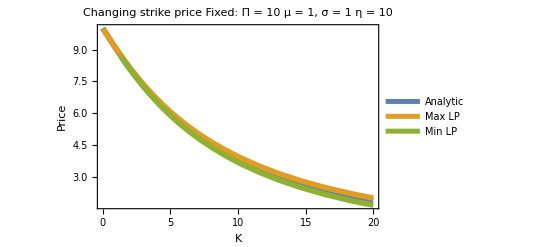

```mathematica
regularization = 10;
mu = 1;
sigma = 1;
pi = 10;
strike = 10;

title ="Changing strike price\n Fixed: " <> "Π = "  <> ToString[pi]<> " μ = " <>ToString[mu] <> ", σ = " <>ToString[sigma] <> " η = " <> ToString[regularization] ;

pltstrike3 = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,True, False, Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False, Automatic, Automatic]}, 
{strike, 0, 20}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, 
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01]},
FrameLabel->{"K", "Price"}, 
LabelStyle->{FontSize->13},
Frame->True,PlotLabel->title, PlotPoints->500]
Export[directory <> "pltstrike3.jpg", pltstrike3];
```

for mu =0 there are no solutions  to the optimization problem (see below)

LinearOptimization::nsolc: There are no points that satisfy the constraints.

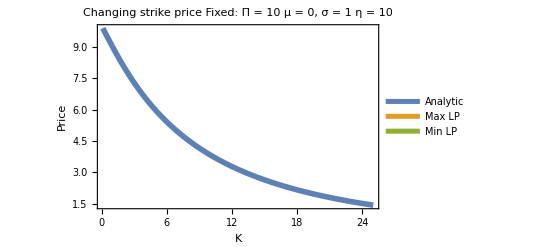

```mathematica
(*regularization = 10;
mu = 0;
sigma = 1;
pi = 10;
strike = 10;

title ="Changing strike price\n Fixed: " <> "Π = "  <> ToString[pi]<> " μ = " <>ToString[mu] <> ", σ = " <>ToString[sigma] <> " η = " <> ToString[regularization] ;

pltstrike4 = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,True, False, Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False, Automatic, Automatic]}, 
{strike, 0.1, 25}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, 
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01]},
FrameLabel->{"K", "Price"}, 
LabelStyle->{FontSize->13},
Frame->True,PlotLabel->title, PlotPoints->500]
Export[directory <> "pltstrike4.jpg", pltstrike4];*)
```

#### Scan the stock price

```mathematica
(*title ="Changing stock price\n Fixed: " <> "μ: " <>ToString[mu] <> ", σ: " <>ToString[sigma] <> ", Z = " <> ToString[strike] <> "Reg = " <> ToString[regularization];
pltstock = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,1],
optimizationPriceBSM[mu, pi, sigma, omegas,strike, regularization,True,False],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False]}, 
{pi, 0.001, 8}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, AxesLabel->{"Π", "Price"}, PlotLabel->title, PlotPoints->500]
Export[directory <> "pltstock.jpg", pltstock];*)

(*title ="Changing stock price\n Fixed: " <> "μ: " <>ToString[mu] <> ", σ: " <>ToString[sigma] <> ", Z = " <> ToString[strike] <> "Reg = " <> ToString[0.1*regularization];
pltstock3 = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,1],
optimizationPriceBSM[mu, pi, sigma, omegas,strike, 0.1*regularization,True,False],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,0.1*regularization,False, False]}, 
{pi, 0.001, 15}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, AxesLabel->{"Π", "Price"},PlotLabel->title, PlotPoints->500]
Export[directory<> "pltstock3.jpg", pltstock3];

title ="Changing stock price\n Fixed: " <> "μ: " <>ToString[mu] <> ", σ: " <>ToString[sigma] <> ", Z = " <> ToString[strike] <> "Reg = " <> ToString[10*regularization];
pltstock4 = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,1],
optimizationPriceBSM[mu, pi, sigma, omegas,strike, 10*regularization,True,False],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,10*regularization,False, False]}, 
{pi, 0.001, 15}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, AxesLabel->{"Π", "Price"}, PlotLabel->title, PlotPoints->500]
Export[directory <> "pltstock4.jpg", pltstock4];*)
```

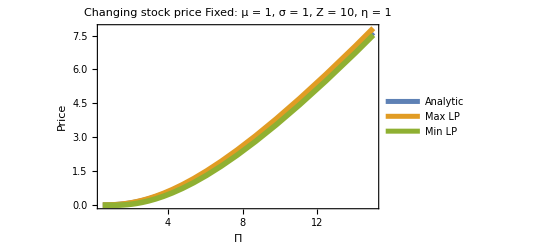

```mathematica
regularization = 1;
mu = 1;
sigma = 1;
pi = 10;
strike = 10;

title ="Changing stock price\n Fixed: " <> "μ = " <>ToString[mu] <> ", σ = " <>ToString[sigma] <> ", Z = " <> ToString[strike] <> ", η = " <> ToString[regularization];

pltstock2 = Plot[
{analyticPriceBSM[ mu, pi,sigma,strike,1,0,0],
optimizationPriceBSM[mu, pi, sigma, omegas,strike, regularization,True,False, Automatic, Automatic],
optimizationPriceBSM[mu, pi, sigma, omegas,strike,regularization,False, False, Automatic, Automatic]}, 
{pi, 0.5, 15}, PlotLegends->{"Analytic", "Max LP", "Min LP"}, 
PlotStyle->{Thickness[0.01], Thickness[0.01], Thickness[0.01]}, 
LabelStyle->{FontSize->13},
Frame->True,
Axes->True,
FrameLabel->{"Π", "Price"}, PlotLabel->title, PlotPoints->500]
Export[directory <> "pltstock2.jpg", pltstock2];
```